## Test Operator with an analytic function

```mathematica
r = Sin[U]Cos[V];
S = r^3 U^4 V^5
```

U^4 V^5 Cos[V]^3 Sin[U]^3

```mathematica
FullSimplify[D[S,U,V]]
```

U^3 V^4 Cos[V]^2 Sin[U]^2 (3 U Cos[U]+4 Sin[U]) (5 Cos[V]-3 V Sin[V])

```mathematica
FullSimplify[D[S,U,V] + (D[r,U]/r)D[S,V] +  (D[r,V]/r)D[S,U]]
```

U^3 V^4 Cos[V]^2 Sin[U]^2 (20 Cos[V] (U Cos[U]+Sin[U])-V (15 U Cos[U]+16 Sin[U]) Sin[V])

```mathematica
FullSimplify[D[S,U]]
```

U^3 V^5 Cos[V]^3 Sin[U]^2 (3 U Cos[U]+4 Sin[U])

```mathematica
FullSimplify[D[S,V]]
```

U^4 V^4 Cos[V]^2 Sin[U]^3 (5 Cos[V]-3 V Sin[V])

```mathematica
FullSimplify[D[Sin[U]^3 U^4,U]]
```

U^3 Sin[U]^2 (3 U Cos[U]+4 Sin[U])

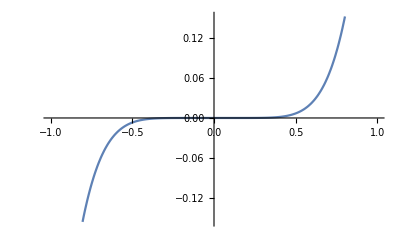

```mathematica
Plot[Sin[U]^3 U^4, {U,-1,1}]
```

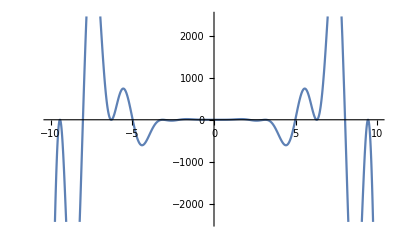

```mathematica
Plot[U^3 Sin[U]^2 (3 U Cos[U]+4 Sin[U]), {U,-10,10}]
```